```mathematica
selldate= {{2010,1,15},{2010,2,18},{2010,5,4},{2010,5,12}};
```

```mathematica
net ={100,150,175,140};
```

```mathematica
trades={{{{2010,1,14},28.69286157666046},{{2010,1,15},28.802756276404608}},{{{2010,2,10},26.745129151291515},{{2010,2,18},27.532485586162714}},{{{2010,2,22},27.632201377108075},{{2010,5,4},35.894830678830985}},{{{2010,5,6},34.65488162436548},{{2010,5,12},35.400814987218126}}}
```

{{{{2010,1,14},28.6929},{{2010,1,15},28.8028}},{{{2010,2,10},26.7451},{{2010,2,18},27.5325}},{{{2010,2,22},27.6322},{{2010,5,4},35.8948}},{{{2010,5,6},34.6549},{{2010,5,12},35.4008}}}

```mathematica
selldate = Transpose[trades][[2]][[All,1]]
```

{{2010,1,15},{2010,2,18},{2010,5,4},{2010,5,12}}

```mathematica
buydate=Transpose[trades][[1]][[All,1]]
```

{{2010,1,14},{2010,2,10},{2010,2,22},{2010,5,6}}

```mathematica
buyprice=Transpose[trades][[1]][[All,2]]
```

{28.6929,26.7451,27.6322,34.6549}

```mathematica
sellprice=Transpose[trades][[2]][[All,2]]
```

{28.8028,27.5325,35.8948,35.4008}

```mathematica
grosProfit=30000;grosLoss=23100;maxDD=1200;netReturn=8.53;
```

```mathematica
aar=8;
```

```mathematica
performance=
Column[
{
Style["Performance",FontSize->14,Bold],
Grid[
{
{
"Net Profit",
"Gros Profit",
"Gros Loss",
"Maximum Drawdown",
"Profit Factor",
"Recovery Factor"
},
{
Row[{Quantity[grosProfit-grosLoss,"Euros"],"(",netReturn,"%)"}],
Quantity[grosProfit,"Euros"],
Quantity[grosLoss,"Euros"],
Quantity[maxDD,"Euros"],
N@grosProfit/grosLoss,
N@(grosProfit-grosLoss)/maxDD
}
},
Background->Lighter[Gray, 0.9],
Frame->All
],
Grid[
{
{
"Annual Average Return",
"Days in Market",
"Risc Adjusted Return",
"Calmar Ratio"
},
{
StringJoin[ToString[80.08],"%"],
StringJoin[ToString[31./127 100],"%"],
StringJoin[ToString[85.08],"%"],
StringJoin[ToString[15.08],"%"]}
},
Background->Lighter[Gray, 0.9],
Frame->All
],
Grid[
{
{
"Buy & Hold Profit",
"Anual Average Buy & Hold",
"Buy & Hold Index"
},
{
StringJoin[ToString[80.08],"%"],
StringJoin[ToString[31./127 100],"%"],
StringJoin[ToString[85.08],"%"]
}
},
Background->Lighter[Gray, 0.9],Frame->All
],
Grid[
{
{
"Total comissions",
"Total slippage",
"Comissions Index"
},
{
StringJoin[ToString[80.08],"%"],
StringJoin[ToString[31./127 100],"%"],
StringJoin[ToString[85.08],"%"]
}
},
Background->Lighter[Gray, 0.9],Frame->All
]
},
Frame->True, Alignment->Center,Background->Lighter[Gray, 0.5],BaseStyle->{FontFamily->"Arial"}
]
```

Performance
Net Profit | Gros Profit | Gros Loss | Maximum Drawdown | Profit Factor | Recovery Factor
6900 €(8.53%) | 30000 € | 23100 € | 1200 € | 1.2987 | 5.75
Annual Average Return | Days in Market | Risc Adjusted Return | Calmar Ratio
80.08% | 24.4094% | 85.08% | 15.08%
Buy & Hold Profit | Anual Average Buy & Hold | Buy & Hold Index
80.08% | 24.4094% | 85.08%
Total comissions | Total slippage | Comissions Index
80.08% | 24.4094% | 85.08%

```mathematica
performance
```

Performance
Net Profit | Gros Profit | Gros Loss | Maximum Drawdown | Profit Factor | Recovery Factor
6900 €(8.53%) | 30000 € | 23100 € | 1200 € | 1.2987 | 5.75
Annual Average Return | Days in Market | Risc Adjusted Return | Calmar Ratio
80.08% | 24.4094% | 85.08% | 15.08%
Buy & Hold Profit | Anual Average Buy & Hold | Buy & Hold Index
80.08% | 24.4094% | 85.08%
Total comissions | Total slippage | Comissions Index
80.08% | 24.4094% | 85.08%

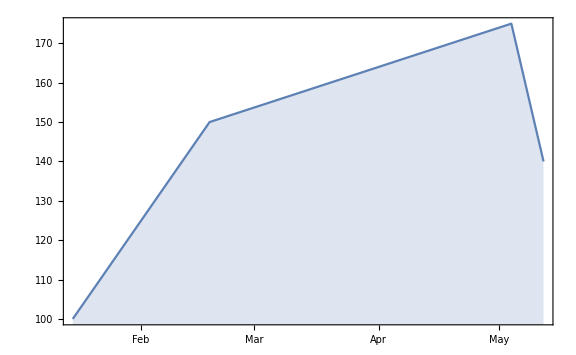
Equity plot:
-Graphics-

```mathematica
plt=Grid[
{{Style["Equity plot:",FontFamily->"Arial"]},
{DateListPlot[Transpose[{selldate,net}],Joined->True,
Filling->0,ImageSize->Large,PlotRange->Full]}}
]
```

```mathematica
table=
Transpose[
{Join[{Style["BuyDate",FontFamily->"Arial"]},DateString[#,"ISODate"]&/@buydate],
Join[{Style["BuyPrice",FontFamily->"Arial"]},buyprice],
Join[{Style["SellDate",FontFamily->"Arial"]},DateString[#,"ISODate"]&/@selldate],
Join[{Style["SellPrice",FontFamily->"Arial"]},sellprice]}
]
```

{{BuyDate,BuyPrice,SellDate,SellPrice},{2010-01-14,28.6929,2010-01-15,28.8028},{2010-02-10,26.7451,2010-02-18,27.5325},{2010-02-22,27.6322,2010-05-04,35.8948},{2010-05-06,34.6549,2010-05-12,35.4008}}

```mathematica
Column[{plt,performance,cost,com,lwt,llt,pos,neg,eq,curr,TableForm[table]},
Frame->All]
```

Equity plot:
-Graphics-
Performance
Net Profit | Gros Profit | Gros Loss | Maximum Drawdown | Profit Factor | Recovery Factor
6900 € | 30000 € | 23100 € | 23100 € | 1.2987 | 1.2987
Annual Average Return | Days in Market | Risc Adjusted Return | Calmar Ratio
80.08% | 24.4094% | 85.08% | 15.08%
Buy & Hold Profit | Anual Average Buy & Hold | Buy & Hold Index
80.08% | 24.4094% | 85.08%
cost
com
lwt
llt
pos
neg
eq
curr
BuyDate | BuyPrice | SellDate | SellPrice
2010-01-14 | 28.6929 | 2010-01-15 | 28.8028
2010-02-10 | 26.7451 | 2010-02-18 | 27.5325
2010-02-22 | 27.6322 | 2010-05-04 | 35.8948
2010-05-06 | 34.6549 | 2010-05-12 | 35.4008